```mathematica
2*(sum sin^2((pi*n)/31) from 1 to 20)-31*sin^2((20*pi)/62)
```

-10 pi sin^2+40/31 from n pi sin^2 sum to

```mathematica
(2*Sum [(Sin[(Pi*n)/31])^2,{n,j}]-31*(Sin[(j*Pi)/62])^2-(Sin[(j*Pi)/31])^2)/30
```

1/30 (-31 Sin[(j π)/62]^2-Sin[(j π)/31]^2+1/2 (1+2 j+Csc[π/31] Sin[1/31 (-π-2 j π)]))

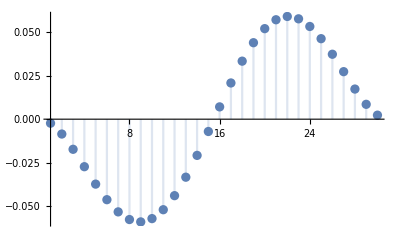

```mathematica
DiscretePlot[1/30 (-31 Sin[(j π)/62]^2-Sin[(j π)/31]^2+1/2 (1+2 j+Csc[π/31] Sin[1/31 (-π-2 j π)])),{j,1,30}]
```

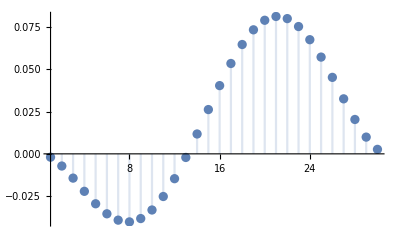

```mathematica
DiscretePlot[1/30 (-31 Sin[(j π)/62]^2+1/2 (1+2 j+Csc[π/31] Sin[1/31 (-π-2 j π)])),{j,1,30}]
```

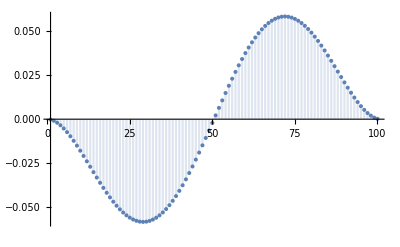

```mathematica
DiscretePlot[(- Sin[(j π)/101]^2-101 Sin[(j π)/202]^2+1/2 (1+2 j+Csc[π/101] Sin[1/101 (-π-2 j π)]))/100,{j,1,100}]
```

```mathematica
N[%10]
```

2.36811

```mathematica
N[%4]
```

12.3471

```mathematica
NumberForm[12.34710965058849,16]
```

12.34710965058849

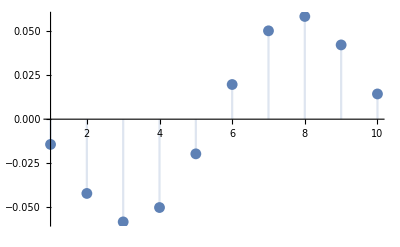

```mathematica
DiscretePlot[(- Sin[(j π)/11]^2-11 Sin[(j π)/22]^2+1/2 (1+2 j+Csc[π/11] Sin[1/11 (-π-2 j π)]))/10,{j,1,10}]
```